# Genetic programming

## Expression representation

```mathematica
GetLabelName[label_]:=Replace[label,Framed[Style[labelName_,___],___]:>labelName];

FunctionToGraph[expr_]:=Block[{tree,labels,functionNames,terminalNames,vertexLabels,order,pos},
tree = ToExpression@ToBoxes@TreeForm[expr];
labels=Cases[tree,Inset[name_,n_]:>Rule[n,GetLabelName[name]],Infinity] /.HoldForm[f_]:>f;
functionNames = DeleteDuplicates@Cases[expr,f_[_,_]:>f,All];
terminalNames = Complement[DeleteDuplicates[labels[[All,2]]],functionNames];
vertexLabels = labels /.Join[Thread[functionNames->Map[Func,functionNames]], Thread[terminalNames->Map[Term,terminalNames]]];

{order,pos}=Catenate/@Cases[tree,Line[order_]|GraphicsComplex[pos_,___]:>{order,pos},Infinity];
{Graph[DirectedEdge@@@order,VertexLabels->labels],vertexLabels}
];
GraphToFunction[edgeList_,vertexLabels_]:=Block[{depthFirstScan},
depthFirstScan = Reverse@First@Last@Reap@DepthFirstScan[edgeList,1,{"PostvisitVertex"->(Sow[#]&)}] /. vertexLabels;

First@FixedPoint[SequenceReplace[#,{Func[f_],Term[y_],Term[x_]}:>Term[f[x,y]]]&,depthFirstScan]/.Term[x_]:>x
];
```

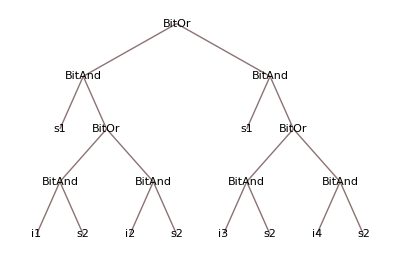

```mathematica
TreeForm[BitOr[BitAnd[s1,BitOr[BitAnd[i3,s2],BitAnd[i4,s2]]],BitAnd[s1,BitOr[BitAnd[i1,s2],BitAnd[i2,s2]]]]]
```

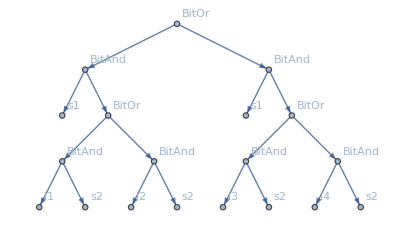
{-Graphics-,{1→Func[BitOr],2→Func[BitAnd],3→Term[s1],4→Func[BitOr],5→Func[BitAnd],6→Term[i1],7→Term[s2],8→Func[BitAnd],9→Term[i2],10→Term[s2],11→Func[BitAnd],12→Term[s1],13→Func[BitOr],14→Func[BitAnd],15→Term[i3],16→Term[s2],17→Func[BitAnd],18→Term[i4],19→Term[s2]}}

```mathematica
FunctionToGraph[BitOr[BitAnd[s1,BitOr[BitAnd[i1,s2],BitAnd[i2,s2]]],BitAnd[s1,BitOr[BitAnd[i3,s2],BitAnd[i4,s2]]]]]
```

```mathematica
GraphToFunction[
-Graphics-,
{1->Func[BitOr],2->Func[BitAnd],3->Term[s1],4->Func[BitOr],5->Func[BitAnd],6->Term[i1],7->Term[s2],8->Func[BitAnd],9->Term[i2],10->Term[s2],11->Func[BitAnd],12->Term[s1],13->Func[BitOr],14->Func[BitAnd],15->Term[i3],16->Term[s2],17->Func[BitAnd],18->Term[i4],19->Term[s2]}
]
```

BitOr[BitAnd[s1,BitOr[BitAnd[i1,s2],BitAnd[i2,s2]]],BitAnd[s1,BitOr[BitAnd[i3,s2],BitAnd[i4,s2]]]]

## Operations on trees

```mathematica
Subtree[graph_,labels_,vertex_]:=Block[{children,toDelete,subtree,sublabels},
children = First@Last@Reap@DepthFirstScan[graph,vertex,{"PrevisitVertex"->(Sow[#]&)}];
toDelete = Complement[VertexList[graph],children];
subtree = VertexDelete[graph,Complement[VertexList[graph],children]];
sublabels = Cases[labels,x_/;MemberQ[children,First[x]]];

{subtree,sublabels}
];
FormatLabels[labels_]:=ReplaceAll[labels,{Term[x_]:>x,Func[x_]:>x}];
DeleteSubtree[graph_,labels_,vertex_]:=Block[{subtree,sublabels,subVertexes,conectionRemoved,withoutSubtree,newLabels},
{subtree,sublabels} = Subtree[graph, labels, vertex];
subVertexes = VertexList[subtree];
conectionRemoved = ReplaceAll[EdgeList[graph],((x_/;!MemberQ[subVertexes,x])->(y_/;MemberQ[subVertexes,y])):>x->Empty];
withoutSubtree = If[Length[Intersection[VertexList[conectionRemoved],subVertexes]]≠ 0,
VertexDelete[conectionRemoved,subVertexes],
conectionRemoved
];
newLabels = Complement[labels,sublabels];

{Graph[withoutSubtree,VertexLabels->FormatLabels[newLabels]],newLabels}
];
InsertSubtree[graph_,labels_,subtree_,sublabels_,subtreeRoot_]:=Block[{edges,missing,missingRules,newRules,insertionRules,formattedSubtree,formattedSublabels,formattedSubtreeRoot,newTree,newLabels},
If[!MemberQ[VertexList[graph],Empty],Return[$Failed]];

edges = DeleteCases[VertexList[graph],Empty];
missing = Complement[Range[Max[edges]],edges];
missingRules = Thread[Take[VertexList[subtree],UpTo[Length[missing]]]->missing];
newRules = Thread[Drop[VertexList[subtree],Length[missing]]-> Range[Max[edges]+1,Max[edges]+Length[VertexList[subtree]]-Length[missing]]];
insertionRules = Join[missingRules,newRules];

formattedSubtree = EdgeList[subtree]/.insertionRules;
formattedSublabels = sublabels/.insertionRules;
formattedSubtreeRoot = subtreeRoot /.insertionRules;
newTree = ReplaceAll[Join[EdgeList[graph],formattedSubtree],Empty->formattedSubtreeRoot];
newLabels = SortBy[Join[labels,formattedSublabels],First];

{Graph[newTree,VertexLabels->FormatLabels[newLabels]],newLabels}
];
```

```mathematica
f1 = LogicOr[LogicAnd[s1,LogicOr[LogicAnd[i3,s2],LogicAnd[i4,s2]]],LogicAnd[s1,LogicOr[LogicAnd[i1,s2],LogicAnd[i2,s2]]]];
f2 = LogicOr[LogicAnd[s1,LogicOr[LogicOr[i3,s2],LogicAnd[i4,s2]]],LogicXor[s1,s2]];
```

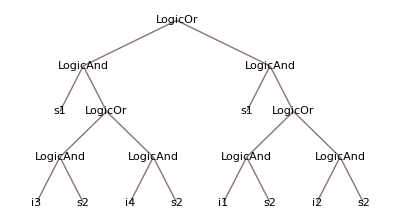
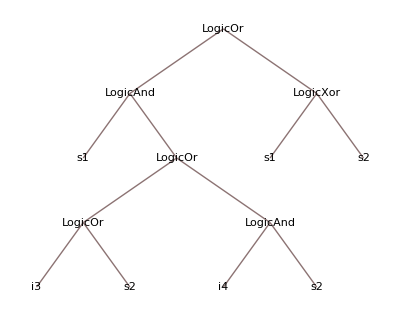

```mathematica
Map[TreeForm,{f1,f2}]
```

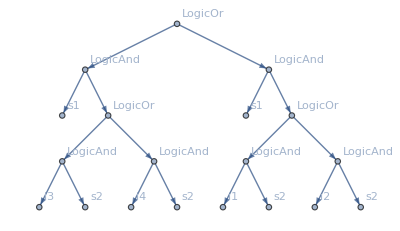
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}}

```mathematica
{g1,l1} = FunctionToGraph[f1]
```

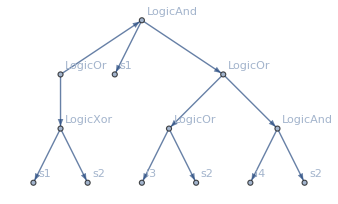
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicOr],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicXor],12→Term[s1],13→Term[s2]}}

```mathematica
{g2,l2} = FunctionToGraph[f2]
```

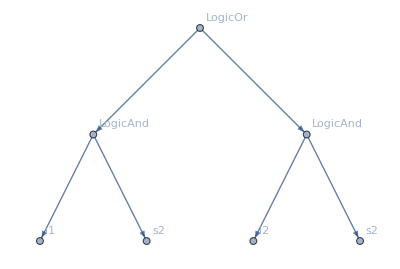
{-Graphics-,{13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}}

```mathematica
{sg1,sl1} = Subtree[g1,l1,13]
```

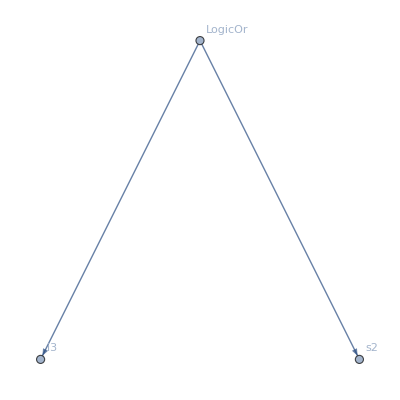
{-Graphics-,{5→Func[LogicOr],6→Term[i3],7→Term[s2]}}

```mathematica
{sg2,sl2} = Subtree[g2,l2,5]
```

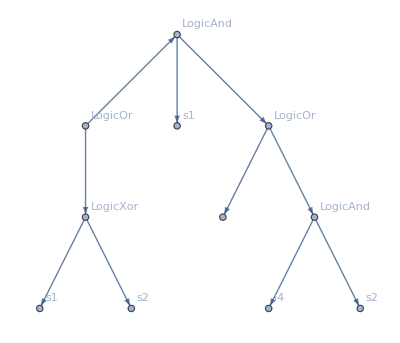
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicXor],12→Term[s1],13→Term[s2]}}

```mathematica
{dst,dl} = DeleteSubtree[g2,l2,5]
```

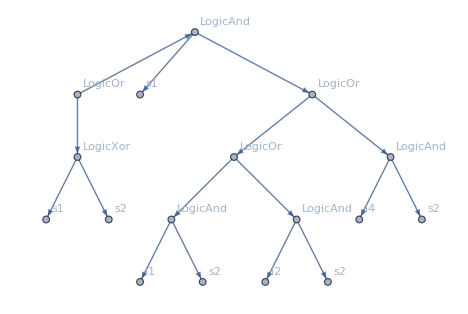
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicOr],6→Func[LogicAnd],7→Func[LogicAnd],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicXor],12→Term[s1],13→Term[s2],14→Term[i1],15→Term[s2],16→Term[i2],17→Term[s2]}}

```mathematica
InsertSubtree[dst,dl,sg1,sl1,13]
```

```mathematica
Apply[GraphToFunction,InsertSubtree[dst,dl,sg1,sl1,13]]
```

LogicOr[LogicAnd[s1,LogicOr[LogicOr[LogicAnd[i1,s2],LogicAnd[i2,s2]],LogicAnd[i4,s2]]],LogicXor[s1,s2]]

## Crossover

```mathematica
Crossover[graph1_,labels1_,graph2_,labels2_]:=Block[{vertex1,vertex2,cropped1,cropped2,sub1,sub2,child1,child2},
vertex1 = RandomChoice[VertexList[graph1]];
vertex2 = RandomChoice[VertexList[graph2]];
cropped1 = DeleteSubtree[graph1,labels1,vertex1];
cropped2 = DeleteSubtree[graph2,labels2,vertex2];
sub1 = Subtree[graph1,labels1,vertex1];
sub2 = Subtree[graph2,labels2,vertex2];
child1 = InsertSubtree[First[cropped1],Last[cropped1],First[sub2],Last[sub2],vertex2];
child2 = InsertSubtree[First[cropped2],Last[cropped2],First[sub1],Last[sub1],vertex1];

{child1,child2}
];
```

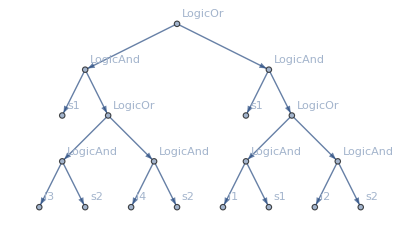
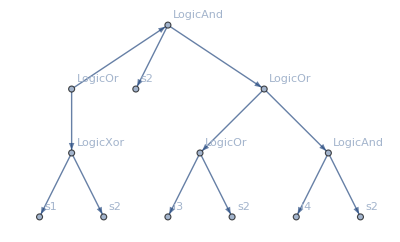
{{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s1],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}},{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s2],4→Func[LogicOr],5→Func[LogicOr],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicXor],12→Term[s1],13→Term[s2]}}}

```mathematica
Crossover[g1,l1,g2,l2]
```